## AirFoils

http : // airfoiltools.com/airfoil/naca4digit

Domains:

0≤x≤1

Max Camber: 0<M<0.095

Max Camber Position: 0<P<0.9

Thickness: 0.01<T<0.40

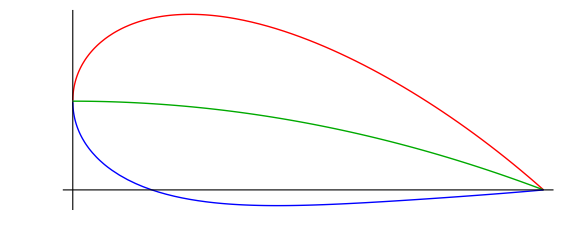

```mathematica
Clear[M,p,yc,T,a0,a1,a2,a3,a4,yt,yc,lower,upper,camber]

(* camber *)
M=0/100; (* M is the maximum camber divided by 100 *)
p=0/10 ; (* p is the position of the maximum camber divided by 4 *)

yc[x_]:=Piecewise[{{M/p^2(2*p*x-x^2),0≤x<p},{M/(1-p)^2(1-2p+2*p*x-x^2),p≤x≤1}}]

(* thickness distribution *)
T=40/100; (* *)

a0=0.2969;
a1=-0.126;
a2=-0.3516;
a3=0.2843;
a4=-0.1015; (* open trainling edge*)
a4=-0.1036; (* closed trainling edge*)
yt[x_]:=T/0.2(a0 √x+a1*x+a2*x^2+a3*x^3+a4*x^4)

θ[x_]:=ArcTan[yc'[x]];

camber[x_]:={x,yc[x]} (* note this could be defined as an explicit function *)
upper[x_]:={x- yt[x]*Sin[θ[x]],yc[x]+yt[x]*Cos[θ[x]]}
lower[x_]:={x + yt[x]*Sin[θ[x]],yc[x]-yt[x]*Cos[θ[x]]}

ParametricPlot[{upper[x],camber[x],lower[x]},{x,0,1},ImageSize->Large,PlotStyle->{{Red,Thick},{Darker[Green],Thick},{Blue,Thick}},PlotPoints->60,Ticks->False]
```

Notice the slight discontinuity at the point p=0.4, which is where the piecewise function is defined.

Typically when integrating a parametric function to determine an area we would use the following:

x=x(t), y=y(t)

Area=∫_0^1 yⅆx=∫_0^1 y(t)ⅆx/ⅆt ⅆt=∫_0^1 y(t)x'(t)ⅆt.

Mathematica has some issues doing the integral exactly (which we don’t need anyway).

No issues doing the integral numerically (integrate to the camber to check things are working correctly):

```mathematica
camber'[x]⟦1⟧
```

1

```mathematica
NIntegrate[upper[x]⟦2⟧upper'[x]⟦1⟧-camber[x]⟦2⟧camber'[x]⟦1⟧,{x,0,1}]
```

0.0688857

```mathematica
NIntegrate[camber[x]⟦2⟧camber'[x]⟦1⟧-lower[x]⟦2⟧lower'[x]⟦1⟧,{x,0,1}]
```

0.0678517

```mathematica
NIntegrate[upper[x]⟦2⟧upper'[x]⟦1⟧-lower[x]⟦2⟧lower'[x]⟦1⟧,{x,0,1}]
```

0.136737

```mathematica
upper'[0.5]⟦1⟧
```

1.00647

## Table of x coordinates of upper, camber, lower as a function of the parameter x (shows these are not the same!)

```mathematica
Table[{upper[x]⟦1⟧,camber[x]⟦1⟧,lower[x]⟦1⟧},{x,0.01,1,0.02}]//TableForm
```

0.010054 | 0.01 | 0.00994605
0.0302698 | 0.03 | 0.0297302
0.0505628 | 0.05 | 0.0494372
0.0709057 | 0.07 | 0.0690943
0.0912837 | 0.09 | 0.0887163
0.111687 | 0.11 | 0.108313
0.132107 | 0.13 | 0.127893
0.152538 | 0.15 | 0.147462
0.172975 | 0.17 | 0.167025
0.193413 | 0.19 | 0.186587
0.213848 | 0.21 | 0.206152
0.234278 | 0.23 | 0.225722
0.254698 | 0.25 | 0.245302
0.275106 | 0.27 | 0.264894
0.2955 | 0.29 | 0.2845
0.315878 | 0.31 | 0.304122
0.336237 | 0.33 | 0.323763
0.356576 | 0.35 | 0.343424
0.376894 | 0.37 | 0.363106
0.397188 | 0.39 | 0.382812
0.417457 | 0.41 | 0.402543
0.4377 | 0.43 | 0.4223
0.457916 | 0.45 | 0.442084
0.478105 | 0.47 | 0.461895
0.498264 | 0.49 | 0.481736
0.518393 | 0.51 | 0.501607
0.538492 | 0.53 | 0.521508
0.558559 | 0.55 | 0.541441
0.578594 | 0.57 | 0.561406
0.598595 | 0.59 | 0.581405
0.618564 | 0.61 | 0.601436
0.638497 | 0.63 | 0.621503
0.658396 | 0.65 | 0.641604
0.678259 | 0.67 | 0.661741
0.698085 | 0.69 | 0.681915
0.717874 | 0.71 | 0.702126
0.737625 | 0.73 | 0.722375
0.757337 | 0.75 | 0.742663
0.777009 | 0.77 | 0.762991
0.79664 | 0.79 | 0.78336
0.81623 | 0.81 | 0.80377
0.835777 | 0.83 | 0.824223
0.855279 | 0.85 | 0.844721
0.874737 | 0.87 | 0.865263
0.894147 | 0.89 | 0.885853
0.91351 | 0.91 | 0.90649
0.932823 | 0.93 | 0.927177
0.952084 | 0.95 | 0.947916
0.971292 | 0.97 | 0.968708
0.990445 | 0.99 | 0.989555

## Animation of Foil as a function of parameters

Note the aspect ratio is incorrect for this.

```mathematica
Clear[M,p,yc,T,a0,a1,a2,a3,a4,yt,yc,lower,upper,camber]

(* camber *)
yc[x_,M_,p_]:=Piecewise[{{M/p^2(2*p*x-x^2),0≤x<p},{M/(1-p)^2(1-2p+2*p*x-x^2),p≤x≤1}}]

(* thickness distribution *)
a0=0.2969;
a1=-0.126;
a2=-0.3516;
a3=0.2843;
a4=-0.1015; (* open trainling edge*)
a4=-0.1036; (* closed trainling edge*)
yt[x_,T_]:=T/0.2(a0 √x+a1*x+a2*x^2+a3*x^3+a4*x^4)

θ[x_,M_,p_]:=ArcTan[Derivative[1,0,0][yc][x,M,p]];

camber[x_,M_,p_]:={x,yc[x,M,p]} (* note this could be defined as an explicit function *)
upper[x_,M_,p_,T_]:={x-yt[x,T]*Sin[θ[x,M,p]],yc[x,M,p]+yt[x,T]*Cos[θ[x,M,p]]}
lower[x_,M_,p_,T_]:={x+yt[x,T]*Sin[θ[x,M,p]],yc[x,M,p]-yt[x,T]*Cos[θ[x,M,p]]}

Manipulate[

ParametricPlot[{upper[x,M,p,T],camber[x,M,p],lower[x,M,p,T]},{x,0,1},ImageSize->Large,PlotStyle->{{Red,Thick},{Darker[Green],Thick},{Blue,Thick}},PlotPoints->60,Ticks->False,PlotRange->{All,{-0.2,0.3}}]

,{M,0.001,0.08,0.001},{T,0.01,0.4,0.005},{p,0.01,0.9,0.001}]
```